```mathematica
metric={{gtt,0,0,0},{0,grr,0,0},{0,0,gθθ,0},{0,0,0,gϕϕ}}//MatrixForm
```

(gtt | 0 | 0 | 0
0 | grr | 0 | 0
0 | 0 | gθθ | 0
0 | 0 | 0 | gϕϕ)

```mathematica
Inverse[{{gtt,0,0,0},{0,grr,0,0},{0,0,gθθ,0},{0,0,0,gϕϕ}}]//MatrixForm
```

(1/gtt | 0 | 0 | 0
0 | 1/grr | 0 | 0
0 | 0 | 1/gθθ | 0
0 | 0 | 0 | 1/gϕϕ)

```mathematica
Clear["Global`*"];
(*Version 0.2.1*)
```

# Einstein Field Equations

## Input Section

```mathematica
Coordinates={t,r,θ,ϕ};
co[μ_]:=Coordinates[[μ]]; (*To simplify the Code*)
Dim=Length[Coordinates];(*Dimention of Space-Time*)
PoM=τ; (*Parameter of Motion*)
ω[r]=1-((2*M *r - Q^2)*r^2)/(r^4 + (2*M *r + Q^2)*l^2);
v[r]=1/ω[r];
Metric(*Subscript[g, μν]*)={{-ω[r],0,0,0},
                              {0,v[r],0,0},
                              {0,0,r^2,0},
                              {0,0,0,r^2 Sin[θ]^2}};
SETensor(*Subscript[T, μν]*)={{ρ c^2,0,0,0},
                              {0,P,0,0},
                              {0,0,P,0},
                              {0,0,0,P}};
MetricInverse=Simplify[Inverse[Metric]];
pdConv[f_]:=TraditionalForm[
f/.Derivative[inds__][g_][vars__]:>
Apply[Defer[D[g[vars],##]]&,
Transpose[{{vars},{inds}}]/.
{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

## Christoffel symbols ( 2_nd kind ) ((Γ^β)_μν)

```mathematica
Christoffel[β_,μ_,ν_]:=Christoffel[β,μ,ν]=Simplify[1/2 Sum[MetricInverse[[β,α]](D[Metric[[α,μ]],co[ν]]+D[Metric[[α,ν]],co[μ]]-D[Metric[[μ,ν]],co[α]]),{α,Dim}]]
```

## Riemann curvature tensor ((R^β)_σμν) & Ricci tensor (R_μν) & Scalar curvature (R)

```mathematica
Riemann[β_,σ_,μ_,ν_]:=Riemann[β,σ,μ,ν]=Simplify[D[Christoffel[β,ν,σ],co[μ]]-D[Christoffel[β,μ,σ],co[ν]]+Sum[Christoffel[β,μ,λ]Christoffel[λ,ν,σ]-Christoffel[β,ν,λ]Christoffel[λ,μ,σ],{λ,Dim}]];
Ricci[μ_,ν_]:=Ricci[μ,ν]=Simplify[Sum[Riemann[λ,μ,λ,ν],{λ,Dim}]];
RicciScalar=Simplify[Sum[Ricci[μ,ν]MetricInverse[[μ,ν]],{μ,Length[Coordinates]},{ν,Dim}]];
```

## Einstein Tensor

```mathematica
EFE[μ_,ν_]:=EFE[μ,ν]=Simplify[Ricci[μ,ν]-1/2 RicciScalar Metric[[μ,ν]]]+Λ Metric[[μ,ν]];
```

## Other Useful Quantities (R_βσμν, R^βσμν, Kretschmann scalar)

```mathematica
Riemanndddd[β_,σ_,μ_,ν_](*Subscript[R, βσμν]*):=Riemanndddd[β,σ,μ,ν]=Sum[Riemann[β1,σ,μ,ν]Metric[[β1,β]],{β1,Dim}]//Simplify;
Riemannuuuu[β_,σ_,μ_,ν_](*R^βσμν*):=Riemannuuuu[β,σ,μ,ν]=Sum[Riemann[β,σ1,μ1,ν1]MetricInverse[[σ1,σ]]MetricInverse[[μ1,μ]]MetricInverse[[ν1,ν]],{σ1,Dim},{μ1,Dim},{ν1,Dim}]//Simplify;
Kretschmann=Sum[Riemanndddd[β,σ,μ,ν]Riemannuuuu[β,σ,μ,ν],{β,Dim},{σ,Dim},{μ,Dim},{ν,Dim}]//Simplify;
```

## Geodesic Equations

```mathematica
Geo=Array[geo,Dim];
For[λ=1,λ<=Dim,λ++,
Geo[[λ]]=Simplify[D[co[λ][PoM],{PoM,2}]+Sum[(Christoffel[λ,μ,ν]/.(#->#[PoM]&/@Coordinates))D[co[μ][PoM],PoM]D[co[ν][PoM],PoM],{μ,Dim},{ν,Dim}]==0]
]
```

## Results

```mathematica
Grid[{{"Metric Tensor (g_μν) = ",MatrixForm[Metric]}},Frame->True,FrameStyle->Blue]
Grid[{{"Inverse Metric Tensor (g^μν) = ",MatrixForm[MetricInverse]}},Frame->True,FrameStyle->Blue]
Grid[{{"Stress-Energy Tensor (T_μν) = ",MatrixForm[SETensor]}},Frame->True,FrameStyle->Blue]
ChristoffelList={{"(Γ^β)_μν",":","Christoffel symbols ( 2 kind )"}};
ChristoffelPrintAction:=AppendTo[ChristoffelList,{Subsuperscript["Γ"," "<>ToString[co[μ]]<>ToString[co[ν]],ToString[co[β]]]," = ",Christoffel[β,μ,ν]//pdConv}];
For[β=1,β<=Dim,β++,
For[μ=1,μ<=Dim,μ++,
For[ν=1,ν<=μ,ν++,
If[Christoffel[β,μ,ν]!=0,
ChristoffelPrintAction,,ChristoffelPrintAction]
]
]
]
If[Length@ChristoffelList==1,ChristoffelList[[1]]={"(Γ^β)_μν","=","Christoffel symbols ( 2 kind ) = 0"}];
Grid[ChristoffelList,Frame->True,FrameStyle->Blue]
RiemannList={{"(R^β)_σμν",":","Riemann curvature tensor"}};
RiemannPrintAction:=AppendTo[RiemannList,{Subsuperscript["R"," "<>ToString[co[σ]]<>ToString[co[μ]]<>ToString[co[ν]],ToString[co[β]]]," = ",Riemann[β,σ,μ,ν]//pdConv}];
For[β=1,β<=Dim,β++,
For[σ=1,σ<=Dim,σ++,
For[μ=1,μ<=Dim,μ++,
For[ν=1,ν<=Dim,ν++,
If[Riemann[β,σ,μ,ν]!=0,
RiemannPrintAction,,RiemannPrintAction]
]
]
]
]
If[Length@RiemannList==1,RiemannList[[1]]={"(R^β)_σμν","=","Riemann curvature tensor = 0"}];
Grid[RiemannList,Frame->True,FrameStyle->Blue]
RicciList={{"R_μν",":","Ricci tensor"}};
RicciPrintAction:=AppendTo[RicciList,{Subscript["R",ToString[co[μ]]<>ToString[co[ν]]]," = ",Ricci[μ,ν]//pdConv}];
For[μ=1,μ<=Dim,μ++,
For[ν=1,ν<=μ,ν++,
If[Ricci[μ,ν]!=0,
RicciPrintAction,,RicciPrintAction]
]
]
If[Length@RicciList==1,RicciList[[1]]={"R_μν","=","Ricci tensor = 0"}];
Grid[RicciList,Frame->True,FrameStyle->Blue]
Grid[{{"Scalar curvature (R) = ",RicciScalar//pdConv}},Frame->True,FrameStyle->Blue]
Grid[{{"Kretschmann (Κ) = ",Kretschmann//pdConv}},Frame->True,FrameStyle->Blue]//Simplify
EFEList={{"G","+ Λ","g_μν","=","Einstein Field Equations","= (8  π G)/c^4 T_μν"}};
EFEPrintAction:=AppendTo[EFEList,{Subscript["G",ToString[co[μ]]<>ToString[co[ν]]],"+ Λ ",Subscript["g",ToString[co[μ]]<>ToString[co[ν]]]," = ",{{EFE[μ,ν]//pdConv," = (8  π G)/c^4 ",SETensor[[μ,ν]]//pdConv}}//Grid,Subscript[" = (8  π G)/c^4 T",ToString[co[μ]]<>ToString[co[ν]]]}];
For[μ=1,μ<=Dim,μ++,
For[ν=1,ν<=μ,ν++,
If[EFE[μ,ν]!=0,
EFEPrintAction,,EFEPrintAction]
]
]
If[Length@EFEList==1,EFEList[[1]]={"G","+ Λ","g_μν","=",0,"= (8  π G)/c^4 T_μν"}];
Grid[EFEList,Frame->True,FrameStyle->Blue]

GeoList={{"Geo^λ",":",""}};
GeoPrintAction:=AppendTo[GeoList,{Superscript["Geo"," "<>ToString[co[λ]]]," ≡ ",Geo[[λ]]//pdConv}];
For[λ=1,λ<=Dim,λ++,
If[Geo[[λ]]!=0,
GeoPrintAction,,GeoPrintAction]
]
Grid[GeoList,Frame->True,FrameStyle->Blue]
```

Metric Tensor (g_μν) =  | (-1+(r^2 (-Q^2+2 M r))/(r^4+l^2 (Q^2+2 M r)) | 0 | 0 | 0
0 | 1/(1-(r^2 (-Q^2+2 M r))/(r^4+l^2 (Q^2+2 M r))) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Inverse Metric Tensor (g^μν) =  | (1/(-1+(r^2 (-Q^2+2 M r))/(r^4+l^2 (Q^2+2 M r))) | 0 | 0 | 0
0 | (l^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r)))/(r^4+l^2 (Q^2+2 M r)) | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[θ]^2/r^2)

Stress-Energy Tensor (T_μν) =  | (c^2 ρ | 0 | 0 | 0
0 | P | 0 | 0
0 | 0 | P | 0
0 | 0 | 0 | P)

(Γ^β)_μν | : | Christoffel symbols ( 2 kind )
Γ_rt^t |  =  | (l^2 r (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^5 (M r-Q^2))/((l^2 (2 M r+Q^2)+r^4) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))
Γ_tt^r |  =  | ((l^2 r (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^5 (M r-Q^2)) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))/((l^2 (2 M r+Q^2)+r^4)^3)
Γ_rr^r |  =  | (l^2 r (4 M^2 r^2+2 M Q^2 r-Q^4)+r^5 (Q^2-M r))/((l^2 (2 M r+Q^2)+r^4) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))
Γ_θθ^r |  =  | -(r (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))/(l^2 (2 M r+Q^2)+r^4)
Γ_ϕϕ^r |  =  | -(r sin^2(θ) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))/(l^2 (2 M r+Q^2)+r^4)
Γ_θr^θ |  =  | 1/r
Γ_ϕϕ^θ |  =  | sin(θ) (-cos(θ))
Γ_ϕr^ϕ |  =  | 1/r
Γ_ϕθ^ϕ |  =  | cot(θ)

(R^β)_σμν | : | Riemann curvature tensor
R_rtr^t |  =  | (l^4 (8 M^3 r^3+12 M^2 Q^2 r^2+6 M Q^4 r-Q^6)-4 l^2 r^4 (7 M^2 r^2+3 M Q^2 r-3 Q^4)+r^8 (2 M r-3 Q^2))/((l^2 (2 M r+Q^2)+r^4)^2 (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))
R_rrt^t |  =  | (l^4 (-8 M^3 r^3-12 M^2 Q^2 r^2-6 M Q^4 r+Q^6)+4 l^2 r^4 (7 M^2 r^2+3 M Q^2 r-3 Q^4)+r^8 (3 Q^2-2 M r))/((l^2 (2 M r+Q^2)+r^4)^2 (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))
R_θtθ^t |  =  | (l^2 r^2 (4 M^2 r^2+2 M Q^2 r-Q^4)+r^6 (Q^2-M r))/((l^2 (2 M r+Q^2)+r^4)^2)
R_θθt^t |  =  | (r (l^2 r (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^5 (M r-Q^2)))/((l^2 (2 M r+Q^2)+r^4)^2)
R_ϕtϕ^t |  =  | -(r sin^2(θ) (l^2 r (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^5 (M r-Q^2)))/((l^2 (2 M r+Q^2)+r^4)^2)
R_ϕϕt^t |  =  | (r sin^2(θ) (l^2 r (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^5 (M r-Q^2)))/((l^2 (2 M r+Q^2)+r^4)^2)
R_ttr^r |  =  | 1/((l^2 (2 M r+Q^2)+r^4)^4)(l^6 (16 M^4 r^4+32 M^3 Q^2 r^3+24 M^2 Q^4 r^2+4 M Q^6 r-Q^8)-l^4 r^2 (16 M^3 r^4 (M+3 r)+8 M^2 Q^2 r^3 (2 M+5 r)-Q^6 r (8 M+11 r)-18 M Q^4 r^3+Q^8)+l^2 r^6 (8 M^2 r^3 (7 M-3 r)+9 Q^4 r (r-4 M)-4 M Q^2 r^2 (M+4 r)+12 Q^6)+r^10 (Q^2 r (8 M-3 r)+2 M r^2 (r-2 M)-3 Q^4))
R_trt^r |  =  | 1/((l^2 (2 M r+Q^2)+r^4)^4)(l^6 (-16 M^4 r^4-32 M^3 Q^2 r^3-24 M^2 Q^4 r^2-4 M Q^6 r+Q^8)+l^4 r^2 (16 M^3 r^4 (M+3 r)+8 M^2 Q^2 r^3 (2 M+5 r)-Q^6 r (8 M+11 r)-18 M Q^4 r^3+Q^8)+l^2 r^6 (8 M^2 r^3 (3 r-7 M)+9 Q^4 r (4 M-r)+4 M Q^2 r^2 (M+4 r)-12 Q^6)+r^10 (Q^2 r (3 r-8 M)+2 M r^2 (2 M-r)+3 Q^4))
R_θrθ^r |  =  | (l^2 r^2 (4 M^2 r^2+2 M Q^2 r-Q^4)+r^6 (Q^2-M r))/((l^2 (2 M r+Q^2)+r^4)^2)
R_θθr^r |  =  | (l^2 r^2 (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^6 (M r-Q^2))/((l^2 (2 M r+Q^2)+r^4)^2)
R_ϕrϕ^r |  =  | -(r^2 sin^2(θ) (l^2 (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^4 (M r-Q^2)))/((l^2 (2 M r+Q^2)+r^4)^2)
R_ϕϕr^r |  =  | (r^2 sin^2(θ) (l^2 (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^4 (M r-Q^2)))/((l^2 (2 M r+Q^2)+r^4)^2)
R_ttθ^θ |  =  | -((l^2 (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^4 (M r-Q^2)) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))/((l^2 (2 M r+Q^2)+r^4)^3)
R_tθt^θ |  =  | ((l^2 (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^4 (M r-Q^2)) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))/((l^2 (2 M r+Q^2)+r^4)^3)
R_rrθ^θ |  =  | (l^2 (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^4 (M r-Q^2))/((l^2 (2 M r+Q^2)+r^4) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))
R_rθr^θ |  =  | (l^2 (4 M^2 r^2+2 M Q^2 r-Q^4)+r^4 (Q^2-M r))/((l^2 (2 M r+Q^2)+r^4) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))
R_ϕθϕ^θ |  =  | (r^2 sin^2(θ) (2 M r-Q^2))/(l^2 (2 M r+Q^2)+r^4)
R_ϕϕθ^θ |  =  | (r^2 sin^2(θ) (Q^2-2 M r))/(l^2 (2 M r+Q^2)+r^4)
R_ttϕ^ϕ |  =  | -((l^2 (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^4 (M r-Q^2)) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))/((l^2 (2 M r+Q^2)+r^4)^3)
R_tϕt^ϕ |  =  | ((l^2 (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^4 (M r-Q^2)) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))/((l^2 (2 M r+Q^2)+r^4)^3)
R_rrϕ^ϕ |  =  | (l^2 (-4 M^2 r^2-2 M Q^2 r+Q^4)+r^4 (M r-Q^2))/((l^2 (2 M r+Q^2)+r^4) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))
R_rϕr^ϕ |  =  | (l^2 (4 M^2 r^2+2 M Q^2 r-Q^4)+r^4 (Q^2-M r))/((l^2 (2 M r+Q^2)+r^4) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))
R_θθϕ^ϕ |  =  | (r^2 (Q^2-2 M r))/(l^2 (2 M r+Q^2)+r^4)
R_θϕθ^ϕ |  =  | (r^2 (2 M r-Q^2))/(l^2 (2 M r+Q^2)+r^4)

R_μν | : | Ricci tensor
R_tt |  =  | (l^6 (-48 M^4 r^4-80 M^3 Q^2 r^3-40 M^2 Q^4 r^2+3 Q^8)+l^4 r^2 (24 M^3 r^4 (2 M+r)+8 M^2 Q^2 r^3 (4 M+r)-3 Q^6 r (4 M+3 r)-8 M Q^4 r^2 (2 M+3 r)+3 Q^8)+l^2 r^6 (24 M^2 r^3 (r-2 M)+Q^4 r (30 M-11 r)+4 M Q^2 r^2 (3 M+2 r)-12 Q^6)+Q^2 r^10 (r (r-2 M)+Q^2))/((l^2 (2 M r+Q^2)+r^4)^4)
R_rr |  =  | (l^4 (24 M^3 r^3+28 M^2 Q^2 r^2+6 M Q^4 r-3 Q^6)-6 l^2 r^4 (4 M^2 r^2+M Q^2 r-2 Q^4)-Q^2 r^8)/((l^2 (2 M r+Q^2)+r^4)^2 (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))
R_θθ |  =  | (l^2 r^2 (12 M^2 r^2+4 M Q^2 r-3 Q^4)+Q^2 r^6)/((l^2 (2 M r+Q^2)+r^4)^2)
R_ϕϕ |  =  | (r^2 sin^2(θ) (l^2 (12 M^2 r^2+4 M Q^2 r-3 Q^4)+Q^2 r^4))/((l^2 (2 M r+Q^2)+r^4)^2)

Scalar curvature (R) =  | (4 l^2 (l^2 (24 M^3 r^3+24 M^2 Q^2 r^2+2 M Q^4 r-3 Q^6)-6 M^2 r^6+5 Q^4 r^4))/((l^2 (2 M r+Q^2)+r^4)^3)

Kretschmann (Κ) =  | 1/((l^2 (2 M r+Q^2)+r^4)^6)8 (l^8 (192 M^6 r^6+384 M^5 Q^2 r^5+240 M^4 Q^4 r^4+16 M^3 Q^6 r^3-28 M^2 Q^8 r^2-4 M Q^10 r+3 Q^12)-2 l^6 r^4 (48 M^5 r^5+120 M^4 Q^2 r^4+76 M^3 Q^4 r^3-38 M^2 Q^6 r^2-38 M Q^8 r+5 Q^10)+2 l^4 r^8 (216 M^4 r^4+180 M^3 Q^2 r^3-131 M^2 Q^4 r^2-80 M Q^6 r+37 Q^8)+2 l^2 r^12 (-24 M^3 r^3+24 M^2 Q^2 r^2+34 M Q^4 r-17 Q^6)+r^16 (6 M^2 r^2-12 M Q^2 r+7 Q^4))

G | + Λ | g_μν | = | Einstein Field Equations | = (8  π G)/c^4 T_μν
G_tt | + Λ  | g_tt |  =  | Λ ((r^2 (2 M r-Q^2))/(l^2 (2 M r+Q^2)+r^4)-1)+(l^4 (24 M^3 r^3+20 M^2 Q^2 r^2-2 M Q^4 r-3 Q^6)+l^2 r^2 (12 M^2 r^3 (r-2 M)+2 Q^4 r (5 M-r)+2 M Q^2 r^2 (2 M+3 r)-3 Q^6)+Q^2 r^6 (r (r-2 M)+Q^2))/((l^2 (2 M r+Q^2)+r^4)^3) |  = (8  π G)/c^4  | c^2 ρ | (= (8  π G)/c^4 T)_tt
G_rr | + Λ  | g_rr |  =  | (l^2 (-12 M^2 r^2-4 M Q^2 r+3 Q^4)-Q^2 r^4)/((l^2 (2 M r+Q^2)+r^4) (l^2 (2 M r+Q^2)+r^2 (r (r-2 M)+Q^2)))+Λ/(1-(r^2 (2 M r-Q^2))/(l^2 (2 M r+Q^2)+r^4)) |  = (8  π G)/c^4  | P | (= (8  π G)/c^4 T)_rr
G_θθ | + Λ  | g_θθ |  =  | (r^2 (l^4 (-24 M^3 r^3-28 M^2 Q^2 r^2-6 M Q^4 r+3 Q^6)+6 l^2 r^4 (4 M^2 r^2+M Q^2 r-2 Q^4)+Q^2 r^8))/((l^2 (2 M r+Q^2)+r^4)^3)+Λ r^2 |  = (8  π G)/c^4  | P | (= (8  π G)/c^4 T)_θθ
G_ϕϕ | + Λ  | g_ϕϕ |  =  | (r^2 sin^2(θ) (l^4 (-24 M^3 r^3-28 M^2 Q^2 r^2-6 M Q^4 r+3 Q^6)+6 l^2 r^4 (4 M^2 r^2+M Q^2 r-2 Q^4)+Q^2 r^8))/((l^2 (2 M r+Q^2)+r^4)^3)+Λ r^2 sin^2(θ) |  = (8  π G)/c^4  | P | (= (8  π G)/c^4 T)_ϕϕ

Geo^λ | : | 
Geo^t |  ≡  | (2 (∂r(τ))/(∂τ) (∂t(τ))/(∂τ) (l^2 r(τ) (-4 M^2 (r(τ))^2-2 M Q^2 r(τ)+Q^4)+(r(τ))^5 (M r(τ)-Q^2)))/((l^2 (2 M r(τ)+Q^2)+(r(τ))^4) (l^2 (2 M r(τ)+Q^2)+(r(τ))^2 (-2 M r(τ)+Q^2+(r(τ))^2)))+(∂^2 t(τ))/(∂τ^2)==0
Geo^r |  ≡  | (((∂t(τ))/(∂τ))^2 (l^2 (2 M r(τ)+Q^2)+(r(τ))^2 (-2 M r(τ)+Q^2+(r(τ))^2)) (l^2 r(τ) (-4 M^2 (r(τ))^2-2 M Q^2 r(τ)+Q^4)+(r(τ))^5 (M r(τ)-Q^2)))/((l^2 (2 M r(τ)+Q^2)+(r(τ))^4)^3)+(((∂r(τ))/(∂τ))^2 (l^2 r(τ) (4 M^2 (r(τ))^2+2 M Q^2 r(τ)-Q^4)+(r(τ))^5 (Q^2-M r(τ))))/((l^2 (2 M r(τ)+Q^2)+(r(τ))^4) (l^2 (2 M r(τ)+Q^2)+(r(τ))^2 (-2 M r(τ)+Q^2+(r(τ))^2)))+(∂^2 r(τ))/(∂τ^2)==(r(τ) (sin^2(θ(τ)) ((∂ϕ(τ))/(∂τ))^2+((∂θ(τ))/(∂τ))^2) (2 l^2 M r(τ)+l^2 Q^2-2 M (r(τ))^3+Q^2 (r(τ))^2+(r(τ))^4))/(2 l^2 M r(τ)+l^2 Q^2+(r(τ))^4)
Geo^θ |  ≡  | sin(θ(τ)) cos(θ(τ)) ((∂ϕ(τ))/(∂τ))^2==(∂^2 θ(τ))/(∂τ^2)+(2 (∂θ(τ))/(∂τ) (∂r(τ))/(∂τ))/(r(τ))
Geo^ϕ |  ≡  | 2 (∂θ(τ))/(∂τ) cot(θ(τ)) (∂ϕ(τ))/(∂τ)+(2 (∂r(τ))/(∂τ) (∂ϕ(τ))/(∂τ))/(r(τ))+(∂^2 ϕ(τ))/(∂τ^2)==0

## Kretschman scalar nature for Hayward Charged Bh and plot

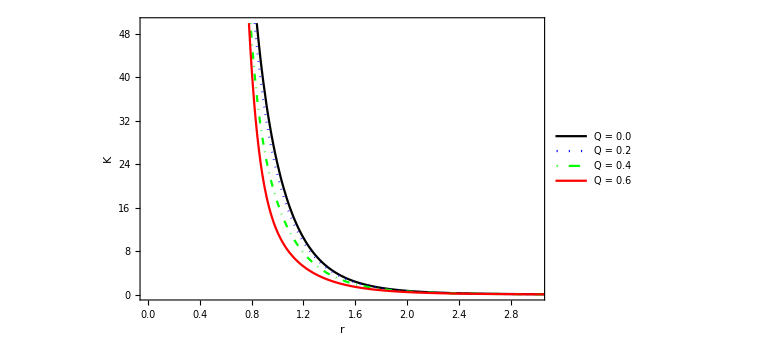

```mathematica
k[Q_,l_,M_,r_] := 1/((l^2 (2 M r+Q^2)+r^4)^6)8 (l^8 (192 M^6 r^6+384 M^5 Q^2 r^5+240 M^4 Q^4 r^4+16 M^3 Q^6 r^3-28 M^2 Q^8 r^2-4 M Q^10 r+3 Q^12)-2 l^6 r^4 (48 M^5 r^5+120 M^4 Q^2 r^4+76 M^3 Q^4 r^3-38 M^2 Q^6 r^2-38 M Q^8 r+5 Q^10)+2 l^4 r^8 (216 M^4 r^4+180 M^3 Q^2 r^3-131 M^2 Q^4 r^2-80 M Q^6 r+37 Q^8)+2 l^2 r^12 (-24 M^3 r^3+24 M^2 Q^2 r^2+34 M Q^4 r-17 Q^6)+r^16 (6 M^2 r^2-12 M Q^2 r+7 Q^4))

Plot[{k[0.0,0.2,1,r],k[0.2,0.2,1,r],k[0.4,0.2,1,r],k[0.6,0.2,1,r]}, {r,0,5},FrameLabel->{"r", "K","l=0.2"},PlotLegends->Placed[{"Q = 0.0 ","Q = 0.2","Q = 0.4", "Q = 0.6"},{Scaled[{0.65,0.78}],{0,0.5}}],Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotStyle->{{Black},{Dotted, Blue},{DotDashed,Green},{Dashing,Red}},PlotRange->{{0,3},{-0.0,50}}]
```

```mathematica
1/((l^2 (2 M r+Q^2)+r^4)^6)8 (l^8 (192 M^6 r^6+384 M^5 Q^2 r^5+240 M^4 Q^4 r^4+16 M^3 Q^6 r^3-28 M^2 Q^8 r^2-4 M Q^10 r+3 Q^12)-2 l^6 r^4 (48 M^5 r^5+120 M^4 Q^2 r^4+76 M^3 Q^4 r^3-38 M^2 Q^6 r^2-38 M Q^8 r+5 Q^10)+2 l^4 r^8 (216 M^4 r^4+180 M^3 Q^2 r^3-131 M^2 Q^4 r^2-80 M Q^6 r+37 Q^8)+2 l^2 r^12 (-24 M^3 r^3+24 M^2 Q^2 r^2+34 M Q^4 r-17 Q^6)+r^16 (6 M^2 r^2-12 M Q^2 r+7 Q^4))/.{Q->0,l->0}
```

(48 M^2)/r^6